## Unit cell transformations

```mathematica
ClearAll["Global`*"]
ReinstallJava[CommandLine -> "java", JVMArguments -> "-Xmx2048m"];
```

```mathematica
(*Calculation of deformated unit cell (cell2) from a given primitive cell (cell1) and strain tensor (ST)and strain tensor for two given unit cells. The linear langrangian strain tensor is calculated acording to the formulation in J.L.Shlenker, G.V.Gibbs and M.B.Boisen, Strain-Tensor components expressend in terms of lattice parameters*)
```

```mathematica
(*Cero: Unit cell x Strain matrix*)
```

```mathematica
cell1={a1,b1,c1,α1,β1,γ1};
```

```mathematica
a1=13.4640;
b1=14.7380;
c1=22.68;
α1=90.0Degree;
β1=90.0Degree;
γ1=123.18Degree;
```

```mathematica
RT1=({{a1, 0, 0}, {b1*Cos[γ1], b1*Sin[γ1], 0}, {c1*Cos[β1], c1*((Cos[α1]-Cos[β1]*Cos[γ1])/Sin[γ1]), (a1 * b1 *  c1 √(1-Cos[α1]^2-Cos[β1]^2-Cos[γ1]^2+2 * Cos[α1]*Cos[β1]*Cos[γ1]))/(a1* b1 *Sin[γ1])}});
```

```mathematica
V1=a1 * b1 *  c1√(1-Cos[α1]^2-Cos[β1]^2-Cos[γ1]^2+2 * Cos[α1]*Cos[β1]*Cos[γ1])
```

3766.67

```mathematica
ST=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
RT2=RT1.ST//MatrixForm
```

(13.464 | 0. | 0.
-8.06568 | 12.335 | 0.
1.38875×10^-15 | 2.56737×10^-15 | 22.68)

```mathematica
xx=39.230;
xy=-16.794862;
yy=24.1088;
xz=1.62651;
yz=-0.5891;
zz=24.0830;
```

```mathematica
Solve[{xy==b*Cos[γ],yy==b*Sin[γ],xz==c*Cos[β],yz==c*((Cos[α]-Cos[β]*Cos[γ])/Sin[γ]),zz==(a *b*  c √(1-Cos[α]^2-Cos[β]^2-Cos[γ]^2+2 * Cos[α]*Cos[β]*Cos[γ]))/(a* b *Sin[γ])},{b,c,γ,α,β}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{b→-29.382,c→-24.1451,γ→-0.962337,α→-1.62935,β→-1.63821},{b→-29.382,c→-24.1451,γ→-0.962337,α→-1.62935,β→1.63821},{b→-29.382,c→-24.1451,γ→-0.962337,α→1.62935,β→-1.63821},{b→-29.382,c→-24.1451,γ→-0.962337,α→1.62935,β→1.63821},{b→29.382,c→24.1451,γ→2.17926,α→-1.62935,β→-1.50338},{b→29.382,c→24.1451,γ→2.17926,α→-1.62935,β→1.50338},{b→29.382,c→24.1451,γ→2.17926,α→1.62935,β→-1.50338},{b→29.382,c→24.1451,γ→2.17926,α→1.62935,β→1.50338}}

```mathematica
α=1.62935;
β=1.50338;
γ=2.17926;
angle1=α*180/Pi
angle2=β*180/Pi
angle2=β*180/Pi
```

```mathematica
(*First we calculate the final deformed cell under a give strain. Do not pay attention to the errors that are given by the program!!*)
```

```mathematica
(*Definition of the unit cell1 (primitive) and cell2(deformed), and their correspondient lattice vectors (or root tensor (RT)). The volume is equal to the numerator of the 33 component. The linear langrangian strain tensor is calculated. *)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
cell1={a1,b1,c1,α1,β1,γ1};
```

```mathematica
cell2={a2,b2,c2,α2,β2,γ2};
```

```mathematica
RT1=({{a1, 0, 0}, {b1*Cos[γ1], b1*Sin[γ1], 0}, {c1*Cos[β1], c1*((Cos[α1]-Cos[β1]*Cos[γ1])/Sin[γ1]), (a1 * b1 *  c1 √(1-Cos[α1]^2-Cos[β1]^2-Cos[γ1]^2+2 * Cos[α1]*Cos[β1]*Cos[γ1]))/(a1* b1 *Sin[γ1])}});
```

```mathematica
V1=a1 * b1 *  c1√(1-Cos[α1]^2-Cos[β1]^2-Cos[γ1]^2+2 * Cos[α1]*Cos[β1]*Cos[γ1])
```

10700.

```mathematica
RT2=({{a2, 0, 0}, {b2*Cos[γ2], b2 * Sin[γ2], 0}, {c2*Cos[β2], c2*((Cos[α2]-Cos[β2]* Cos[γ2])/Sin[γ2]), (a2 * b2 * c2 √(1-Cos[α2]^2-Cos[β2]^2-Cos[γ2]^2+2*Cos[α2]*Cos[β2]*Cos[γ2]))/(a2* b2*Sin[γ2])}});
```

```mathematica
V2=a2 * b2 * c2√(1-Cos[α2]^2-Cos[β2]^2-Cos[γ2]^2+2*Cos[α2]*Cos[β2]*Cos[γ2]);
```

```mathematica
ST=1/2(Transpose[Inverse[RT1].RT2]+Inverse[RT1].RT2)-IdentityMatrix[3];
```

```mathematica
(*The copmponents of the strain tensor are then denoted l11, l12, l13 ..., and acording to the previous equation (ommit the ; if you want to see the full results) we get the general result:*)
```

```mathematica
l11=-1+a2/a1;
```

```mathematica
l12=l21=1/2 (-(a2 Cot[γ1])/a1+(b2 Cos[γ2] Csc[γ1])/b1);
```

```mathematica
l13=l31=1/2 ((b2 Cos[γ2] (a1 c1 Cos[β1] Cot[γ1]-a1 c1 Cos[α1] Csc[γ1]))/(a1 b1 c1 √(1-Cos[α1]^2-Cos[β1]^2+2 Cos[α1] Cos[β1] Cos[γ1]-Cos[γ1]^2))+(c2 Cos[β2] Sin[γ1])/(c1 √(1-Cos[α1]^2-Cos[β1]^2+2 Cos[α1] Cos[β1] Cos[γ1]-Cos[γ1]^2))+(a2 (b1 c1 Cos[α1] Cot[γ1]-b1 c1 Cos[β1] Cos[γ1] Cot[γ1]-b1 c1 Cos[β1] Sin[γ1]))/(a1 b1 c1 √(1-Cos[α1]^2-Cos[β1]^2+2 Cos[α1] Cos[β1] Cos[γ1]-Cos[γ1]^2)));
```

```mathematica
l22=-1+(b2 Csc[γ1] Sin[γ2])/b1;
```

```mathematica
l23=l32=1/2 ((c2 (Cos[α2]-Cos[β2] Cos[γ2]) Csc[γ2] Sin[γ1])/(c1 √(1-Cos[α1]^2-Cos[β1]^2+2 Cos[α1] Cos[β1] Cos[γ1]-Cos[γ1]^2))+(b2 (a1 c1 Cos[β1] Cot[γ1]-a1 c1 Cos[α1] Csc[γ1]) Sin[γ2])/(a1 b1 c1 √(1-Cos[α1]^2-Cos[β1]^2+2 Cos[α1] Cos[β1] Cos[γ1]-Cos[γ1]^2)));
```

```mathematica
l33=-1+(c2 √(1-Cos[α2]^2-Cos[β2]^2+2 Cos[α2] Cos[β2] Cos[γ2]-Cos[γ2]^2) Csc[γ2] Sin[γ1])/(c1 √(1-Cos[α1]^2-Cos[β1]^2+2 Cos[α1] Cos[β1] Cos[γ1]-Cos[γ1]^2));
```

## Elastic Tensor calculations

Calculation of the elastic parameters from the elastic matrix coeficients. Bulk modulus, Shear modulus, Young modulus, Poisson ratios. Here we define the values: CM elastic matrix, SM compilance matrix, K bulk modulus, G shear modulus, E young modulus and ν poisson ratio. The index v and r denote Voight and Reuss definitions 
J.F.Nye.Physical properties of crystals.Oxford University Press, (1957). The average is call Hill definition. E and ν are calculated assuming an isotropic media through the standar relationships. M is the stiffness of the material.

Definition of elastic properties from elastic tensor coeficients:

```mathematica
ClearAll["Global`*"]
```

```mathematica
SM=Inverse[CM];
Kv=1/9(c11+c22+c33)+2/9(c12+c13+c23);Kr=1/((s11+s22+s33)+2(s12+s13+s23));
K=(Kv+Kr)/2;
Gv=1/15(c11+c22+c33-c12-c13-c23)+1/5(c44+c55+c66);
Gr=15/(4(s11+s22+s33)-4(s12+s13+s23)+3(s44+s55+s66));
G=(Gv+Gr)/2;
Em=(9 K G)/(3K+G); η=(3K-2G)/(2(3K+G)); M=Em/(1-η^2); M2=4G(3K+G)/(3K+4G);
Ex=1/s11;Ey=1/s22;Ez=1/s33;Ea=(Ex+Ey+Ez)/3;
Gyz=1/s44; Gxz=1/s55; Gyx=1/s66;
vyx=-Ey*s12;vzx=-Ez*s13;vxy=-Ex*s21;
vzy=-Ez*s23;vxz=-Ex*s31; 
vyz=-Ey*s32;
```

START OF THE INPUT. Write the coeficients of the elastic matrix. Then, when the compilance matrix is calculated, re - write the coeficients of the compilance matrix

```mathematica
CM=({{252, 113, 95, 0, 0, 0}, {87, 227, 74, 0, 0, 0}, {61, 92, 231, 0, 0, 0}, {0, 0, 0, 68, 0, 0}, {0, 0, 0, 0, 32, 0}, {0, 0, 0, 0, 0, 72}});
```

```mathematica
c11=CM[[1,1]];c12=c21= CM[[1,2]];c13= c31=CM[[1,3]]; 
c14= c41=CM[[1,4]];c15= c51=CM[[1,5]]; c16= c61=CM[[1,6]];
c22= CM[[2,2]]; c23=c32=CM[[2,3]]; c24= c42=CM[[2,4]];
c25= c52=CM[[2,5]]; c26= c62=CM[[2,6]];
c33= CM[[3,3]];c34= c43=CM[[3,4]];c35= c53=CM[[3,5]];
c36= c63=CM[[3,6]]; 
c44= CM[[4,4]];c45= c54=CM[[4,5]];c46= c64=CM[[4,6]];
c55= CM[[5,5]];c56= c65=CM[[5,6]]; 
c66= CM[[6,6]];
```

The eigenvalues below should all be positive, indicating stability of the crystal.

```mathematica
Eigenvalues[CM]//Reverse//N
```

{32.,68.,72.,139.269,160.868,409.863}

```mathematica
SM//MatrixForm//N
```

(0.0049691 | -0.00189087 | -0.00143784 | 0. | 0. | 0.
-0.00169702 | 0.00570833 | -0.00113073 | 0. | 0. | 0.
-0.000636316 | -0.00177413 | 0.00515903 | 0. | 0. | 0.
0. | 0. | 0. | 0.0147059 | 0. | 0.
0. | 0. | 0. | 0. | 0.03125 | 0.
0. | 0. | 0. | 0. | 0. | 0.0138889)

```mathematica
s11=SM[[1,1]];s12=s21= SM[[1,2]];s13= s31=SM[[1,3]]; 
s14= s41=SM[[1,4]];s15= s51=SM[[1,5]]; s16= s61=SM[[1,6]];
s22= SM[[2,2]]; s23= s32=SM[[2,3]]; s24= s42=SM[[2,4]];
s25= s52=SM[[2,5]]; s26= s62=SM[[2,6]];
s33= SM[[3,3]];s34= s43=SM[[3,4]];s35= s53=SM[[3,5]];
s36= s63=SM[[3,6]]; 
s44= SM[[4,4]];s45= s54=SM[[4,5]];s46= s64=SM[[4,6]];
s55= SM[[5,5]];s56= s65=SM[[5,6]]; 
s66= SM[[6,6]];
```

```mathematica
{{"", Voigt, Reuss, Hill, "", "", ""}, {"Bulk", Kv//N, Kr//N, K//N, "", "", ""}, {"Shear", Gv//N, Gr//N, G//N, "", "", ""}, {"Young", x, y, z, average, elastic, ""}, {"", Ex//N, Ey//N, Ez//N, Ea//N, Em//N, ""}, {"", Poisson, Indentation1, Indentation2, η//N, M//N, ""}, {Shear, xy, yz, xz, "", "", ""}, {"", Gyx//N, Gyz//N, Gxz//N, "", "", ""}, {Poisson, xy, xz, yx, yz, zx, zy}, {"", vxy//N, vxz//N, vyz//N, vyz//N, vzx//N, vzy//N}}//TableForm
```

| Voigt | Reuss | Hill |  |  | 
Bulk | 141.556 | 144.559 | 143.057 |  |  | 
Shear | 62.9333 | 57.5334 | 60.2334 |  |  | 
Young | x | y | z | average | elastic | 
 | 201.244 | 175.183 | 193.835 | 190.087 | 158.461 | 
 | Poisson | Indentation1 | Indentation2 | 0.315388 | 175.964 | 
Shear | xy | yz | xz |  |  | 
 | 72. | 68. | 32. |  |  | 
Poisson | xy | xz | yx | yz | zx | zy
 | 0.380526 | 0.289355 | 0.198085 | 0.198085 | 0.278703 | 0.219175

```mathematica
CORE-SHELL
Mechanical properties:Convention:Reuss Voigt Hill
Bulk  Modulus (GPa)=177.33164 178.01906 177.67535
Shear Modulus (GPa)=90.03637 96.54755 93.29196
Velocity S-wave (km/s)=4.94504 5.12073 5.03365
Velocity P-wave (km/s)=8.98705 9.12752 9.05756
Compressibility (1/GPa)=0.00563915
Stress axis:x y z
Youngs Moduli (GPa)=275.16143 165.76566 249.25356
Poissons Ratio (x)=0.27261 0.04577
Poissons Ratio (y)=0.45252 0.54628
Poissons Ratio (z)=0.05052 0.36330

REAXFF
Mechanical properties:Convention:Reuss Voigt Hill
Bulk Modulus (GPa)=106.35119 110.25834 108.30477
Shear Modulus (GPa)=39.47035 45.30704 42.38869
Velocity S-wave (km/s)=3.38785 3.62970 3.51086
Velocity P-wave (km/s)=6.79919 7.04472 6.92305
Compressibility (1/GPa)=0.00940281
Stress axis:x y z
Youngs Moduli (GPa)=169.72063 106.07496 85.99545
Poissons Ratio (x)=0.21691 0.11238
Poissons Ratio (y)=0.34706 0.46616
Poissons Ratio (z)=0.22180 0.57501
```

## Tensorial analysis of second-order classic constants

From the article: Metal–organic frameworks with wine-rack motif : What determines their flexibility and elastic properties?
ELATE: an open-source online application for analysis and visualization of elastic tensors

### Input: the stiffness matrix (in Voigt or engineering notation)

```mathematica
ClearAll["Global`*"]
```

```mathematica
CM=({{38.5, 19.6, 32.7, 0, -0, -6.1}, {19.6, 127.1, 37.0, 0, 0, -12.1}, {32.7, 37.0, 173.2, 0, 0, -4.5}, {0, 0, 0, 19.5, -2.8, 0}, {0, 0, 0, -2.8, 6.3, 0}, {-6.1, -12.1, -4.5, 0, 0, 5.4}});
```

First we compute the eigenvaluesof the stiffness matrix. They should all be positive, indicating stability of the crystal. The condition is actually that: C_44>0; C_11-C_12>0; C_11+2 C_12>0

```mathematica
Eigenvalues[CM]//Reverse//N
```

{3.6128,5.73062,20.0694,30.1214,107.265,203.201}

### Code for tensorial analysis & calculation of mechanical properties

The block below contains all the code of the notebook. We use it in the next section to plot properties of the material.

```mathematica
SVoigt=Inverse[CM];
VoigtMat={{1,6,5},{6,2,4},{5,4,3}};
SVoigtCoeff[p_,q_]:=1/(Ceiling[p/3]*Ceiling[q/3]);
Smat=Table[SVoigtCoeff[VoigtMat[[i,j]],VoigtMat[[k,l]]]
*SVoigt[[VoigtMat[[i,j]],VoigtMat[[k,l]]]],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
Cmat=Table[CM[[VoigtMat[[i,j]],VoigtMat[[k,l]]]],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}]//MatrixForm;
dirVector[θ_,ϕ_]:={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
```

Young Modulus

```mathematica
YoungModulus[θ_,ϕ_]:=Module[{a},
a=dirVector[θ,ϕ];
1/Sum[a[[i]]*a[[j]]*a[[k]]*a[[l]]*Smat[[i,j,k,l]],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}]];
```

Linear Compressibility

```mathematica
linearCompressibility[θ_,ϕ_]:=Module[{a},
a=dirVector[θ,ϕ];
Sum[a[[i]]*a[[j]]*Smat[[i,j,k,k]],
{i,1,3},{j,1,3},{k,1,3}]];
dirVector2[θ_,ϕ_,χ_]:={Cos[θ]*Cos[ϕ]*Cos[χ]-Sin[ϕ]*Sin[χ],
Cos[θ]*Sin[ϕ]*Cos[χ]+Cos[ϕ]*Sin[χ],-Sin[θ]*Cos[χ]}
```

Shear Modulus

```mathematica
shearModulus[θ_,ϕ_,χ_]:=Module[{a,b},
a=dirVector[θ,ϕ];
b=dirVector2[θ,ϕ,χ];
1/(4*Sum[a[[i]]*b[[j]]*a[[k]]*b[[l]]*Smat[[i,j,k,l]],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}])];
```

Poissons Ratio

```mathematica
PoissonRatio[θ_,ϕ_,χ_]:=Module[{a,b},
a=dirVector[θ,ϕ];
b=dirVector2[θ,ϕ,χ];
-Sum[a[[i]]*a[[j]]*b[[k]]*b[[l]]*Smat[[i,j,k,l]],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}]
/Sum[a[[i]]*a[[j]]*a[[k]]*a[[l]]*Smat[[i,j,k,l]],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}]];
```

### Results of the analysis

First, we focus on directional Young’s modulus. We calculate its minimal and maximal values.

```mathematica
Emax=Maximize[YoungModulus[θ,ϕ],{θ,ϕ}]//N
Emin=Minimize[YoungModulus[θ,ϕ],{θ,ϕ}]//N
```

{116.531,{θ→-1.5708,ϕ→-1.48252}}

{9.18372,{θ→1.5708,ϕ→0.713357}}

Then we do a 3D plot

```mathematica
SphericalPlot3D[YoungModulus[θ,ϕ],θ,ϕ,
PlotRange->All,PlotPoints->60,PerformanceGoal->"Quality",
PlotTheme -> "Scientific",
ColorFunction->(ColorData[{"SunsetColors","Reverse"}][#6]&),
PlotLegends->Automatic,
PlotStyle->Directive[Opacity[0.9],Specularity[White,20]],
Mesh->True,
MeshStyle->Directive[Opacity[0.2]],
Boxed->True,BoxStyle->Dashed,
Axes->True,
AxesLabel->{Style["x",22,Bold],Style["y",22,Bold],Style["z",22,Bold]},
LabelStyle->Directive[Black,15,FontFamily->"Helvetica"]]
```

-Graphics3D-

We compute the Youg moduli in each direction (x, y, z):

```mathematica
{YoungModulus[π/2,0],YoungModulus[π/2,π/2],YoungModulus[0,0]}//N
```

{26.4424,93.7769,140.194}

And finally, a polar plot in the plane of flexibility (zy,xy,xz):

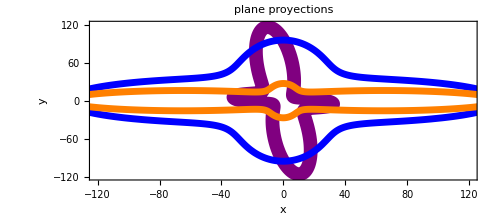

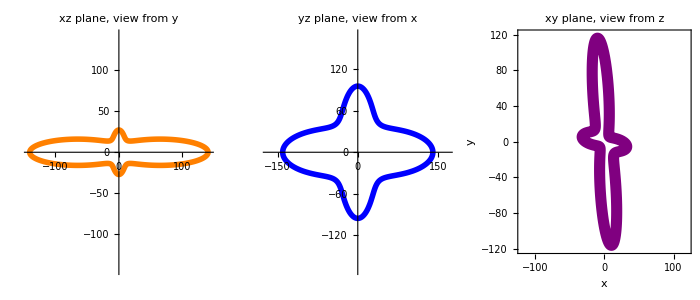

```mathematica
Exz=PolarPlot[YoungModulus[θ,0],{θ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.01],Orange},PlotLabel->"xz plane, view from y"];
Eyz=PolarPlot[YoungModulus[θ,π/2],{θ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.01],Blue},PlotLabel->"yz plane, view from x"];

Exy=PolarPlot[YoungModulus[π/2,ϕ],{ϕ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.02],Purple},Frame->True,FrameStyle-> Black,AxesStyle->Dashed, 
FrameLabel->{Style["x",LineSpacing->{1,1},20],Style["y",LineSpacing->{0,0},20]},FrameTicksStyle->{{{14},None},{{14},None}},PlotLabel->"xy plane, view from z"];

Show[{Exy,Eyz,Exz},PlotLabel->"plane proyections"]
GraphicsGrid[{{Exz,Eyz,Exy}},ImageSize->{700,300}]
```

Linear compressibility and bulk modulus. First, we calculate its minimal and maximal values of linear compresibility and bulk modulus

```mathematica
βmax=Maximize[linearCompressibility[θ,ϕ],{θ,ϕ}]//N
βmin=Minimize[linearCompressibility[θ,ϕ],{θ,ϕ}]//N
```

{0.0478924,{θ→1.5708,ϕ→0.586565}}

{-0.00919054,{θ→-1.5708,ϕ→-0.984231}}

We do a 3 D plot of the linear compresibility (green lobe for positive LC, red lobe for negative LC) :

```mathematica
Show[
SphericalPlot3D[Max[linearCompressibility[θ,ϕ],0],θ,ϕ,PlotStyle->Directive[Green,Opacity[0.7]],PlotRange->All],
SphericalPlot3D[Max[-linearCompressibility[θ,ϕ],0],θ,ϕ,PlotStyle->Directive[Red,Opacity[0.7]]],PlotRange->All,AxesLabel->{x,y,z}]
```

-Graphics3D-

And we characterize the values along each crystallographic axis. The top value is the linear compresibility and the bottom its inverse, essentially a compressibility modulus:

```mathematica
{linearCompressibility[π/2,0],linearCompressibility[π/2,π/2],linearCompressibility[0,0]}//N
```

{0.0316887,0.00887146,-0.000618442}

And a polar plot of the in plane linear incompresibility (zy, xy, xz) :

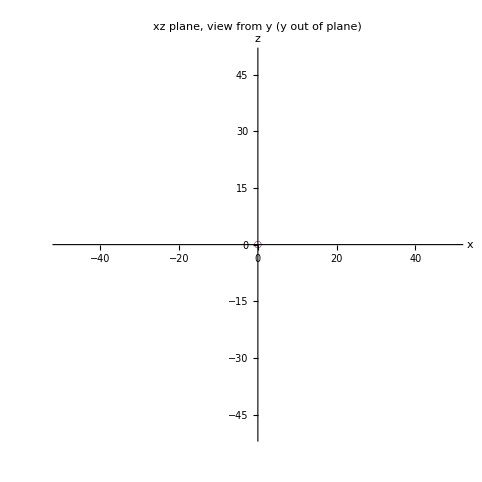

```mathematica
Kxz=PolarPlot[linearCompressibility[θ,0],{θ,0,2π},PlotRange->{{-50,50},{-50,50}},PlotStyle->{Thickness[0.01],Orange},AxesLabel->{x,z},PlotLabel->"xz plane, view from y (y out of plane)"];
Kyz=PolarPlot[linearCompressibility[θ,π/2],{θ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.01],Blue},PlotLabel->"yz plane, view from x"];
Kxy=PolarPlot[linearCompressibility[11,ϕ],{ϕ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.01],Purple},PlotLabel->"xy plane, view from z"];
Show[Kxz,Kyz,Kxy]
```

Minimal and maximal values (and corresponding directions) for shear modulus and Poisson’s ratio:

```mathematica
Minimize[shearModulus[θ,ϕ,χ],{θ,ϕ,χ}]//N
 Maximize[shearModulus[θ,ϕ,χ],{θ,ϕ,χ}]//N
```

{5.73062,{θ→-5.97922×10^-9,ϕ→0.0512441,χ→0.14937}}

{20.0694,{θ→-1.55096×10^-25,ϕ→-0.78253,χ→-0.587652}}

```mathematica
GmaxS=SphericalPlot3D[Max[shearModulus[θ,ϕ,-1.5708]],θ,ϕ,
PlotRange->All,PlotPoints->60,PerformanceGoal->"Quality",
PlotTheme -> "Scientific",
(*ColorFunction->(ColorData[{"SunsetColors","Reverse"}][#6]&),*)
PlotLegends->Automatic,
PlotStyle->Red(*Directive[Opacity[0.7],Specularity[White,20]]*),
Boxed->True,BoxStyle->Dashed,
Axes->True,
AxesLabel->{Style["x",22,Bold],Style["y",22,Bold],Style["z",22,Bold]},
LabelStyle->Directive[Black,15,FontFamily->"Helvetica"]];
GminS=SphericalPlot3D[Max[shearModulus[θ,ϕ,0.0]],θ,ϕ,
PlotStyle->Blue
(*ColorFunction->(ColorData[{"SunsetColors","Reverse"}][#6]&)*)];
Show[{GmaxS,GminS}]
```

-Graphics3D-

And a polar plot of the in plane bulk modulus (zy, xy, xz) :

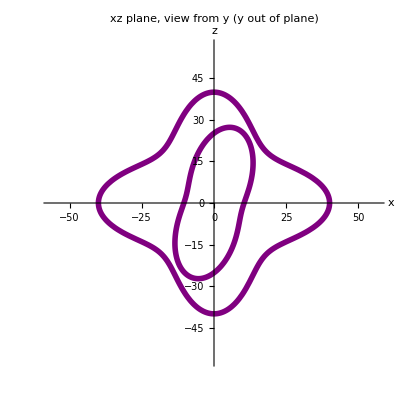

```mathematica
GxzMax=PolarPlot[shearModulus[θ,0,-1.5708],{θ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.01],Orange}];
GxzMin=PolarPlot[shearModulus[θ,0,0.25162],{θ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.01],Orange}];

GyzMax=PolarPlot[shearModulus[θ,π/2,-1.5708],{θ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.01],Blue}];
GyzMin=PolarPlot[shearModulus[θ,π/2,0.25162],{θ,0,2π},PlotRange->All,PlotStyle->{Thickness[0.01],Blue}];

GxyMax=PolarPlot[shearModulus[1.5708,ϕ,-1.5708],{ϕ,0,2π},PlotRange->All,
PlotStyle->{Thickness[0.01],Purple}];
GxyMin=PolarPlot[shearModulus[-0.00006,ϕ,0.25162],{ϕ,0,2π},PlotRange->All,
PlotStyle->{Thickness[0.01],Purple}];

Show[{GxyMax,GxyMin},AxesLabel->{x,z},PlotLabel->"xz plane, view from y (y out of plane)"]
```

```mathematica
Minimize[PoissonRatio[θ,ϕ,χ],{θ,ϕ,χ}]//N
Maximize[PoissonRatio[θ,ϕ,χ],{θ,ϕ,χ}]//N
```

{0.293288,{θ→0.773324,ϕ→1.41724×10^-8,χ→-3.2416×10^-8}}

{0.597515,{θ→-0.780581,ϕ→-4.46761×10^-9,χ→-1.5708}}